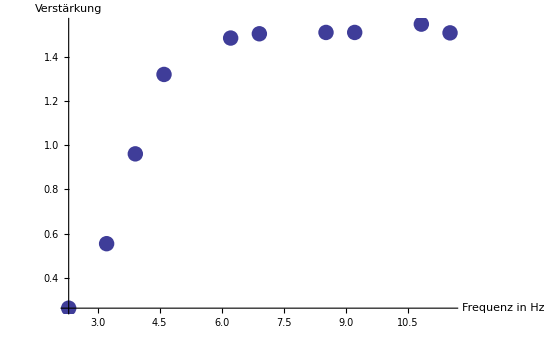

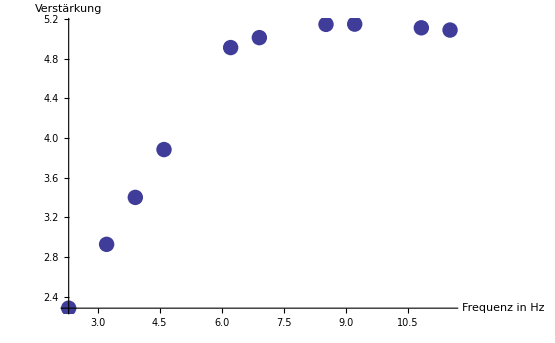

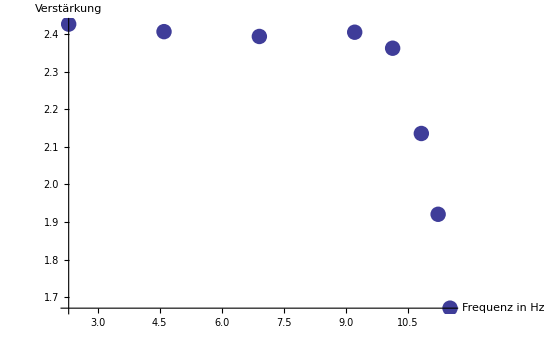

```mathematica
data1:={{10,2/1.54},{25,3.48/2},{50,5.44/2.08},{100,7.8/2.08},{500,9.2/2.08},{1000,9.2/2.04},
{5000,9.8/2.16},{10000,9.8/2.16},{50000,9.8/2.08},{100000,9.6/2.12}};
data2:={{10,3.44/0.35},{25,8.6/0.46},{50,11.4/0.38},{100, 6.8/0.14},{500,7.6/0.056},{1000,8.4/0.056},
{5000,9.6/0.056},{10000,11/0.064},{50000,10.6/0.064},{100000,10.2/0.063}};
data3:={{10,5.84/0.516},{100,5.68/0.512},{1000,5.52/0.504},{10000,5.76/0.52},{25000,5.52/0.52},{50000,4.4/0.52},{75000,3.44/0.504},{100000,2.68/0.504}};

logScale[data_]:=Module[{result={}},
For[i=1,i≤Length[data],i++,
AppendTo[result,{Log[data[[i]][[1]]], Log[data[[i]][[2]]]}]];
result
];

Show[ListPlot[logScale[data1],PlotStyle->{PointSize[0.02]}],{AxesLabel->{"Frequenz in Hz","Verstärkung"}}]
Show[ListPlot[logScale[data2],PlotStyle->{PointSize[0.02]}],{AxesLabel->{"Frequenz in Hz", "Verstärkung"}}]
Show[ListPlot[logScale[data3],PlotStyle->{PointSize[0.02]}],{AxesLabel->{"Frequenz in Hz", "Verstärkung"}}]
```